-Graphics-

## Lesson 6: Separable equations

-Graphics-

## Overview

The previous lesson used a method of direct integration to solve differential equations such as:

y'(t)+a(t) y(t)=b(t)

This method is called separation of variables and can naturally be applied to a wide variety of differential equations, which can even be nonlinear:

y'(t)=t/(y(t))

There is no general method of solving all first-order ODEs, but a large subclass of first-order equations falls under the category of separable.

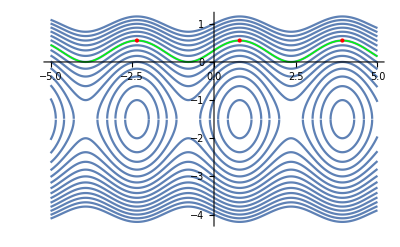

```mathematica
Show[Plot[Table[1/2 (-3+√(9+4 C+4 Sin[2 t])),{C,-4,4,.5}],{t,-5,5}],Plot[Table[1/2 (-3-√(9+4 C+4 Sin[2 t])),{C,-4,4,.5}],{t,-5,5}],Plot[1/2 (-3+√(9+4+4 Sin[2 t])),{t,-5,5},PlotStyle->{Thick,Green}],ListPlot[Table[{t,1/2 (-3+√(9+4+4 Sin[2 t]))},{t,-π+π/4,π+π/4,π}],PlotStyle->{Red,PointSize->Large}],PlotRange->All]
```

## Separation of Variables

Begin with a general first-order differential equation:

y'(t)=f(t,y(t))

If the function f(t,y(t)) can be separated into the form:

f(t,y(t))=(N(t))/(M(y(t)))

then the differential equation can be written as:

M(y(t))ⅆy(t)=N(t)ⅆt

Integration can then be used to obtain:

∫M(y(t))ⅆy(t)=∫N(t)ⅆt+C

When both sides are integrable, the solution is obtained by solving for y(t).

## Classify Equation as Separable

Verify that the following equation is separable, and find the solution:

y'(t)=t/(y(t))

The only way to prove an equation is separable is by means of algebraic operations.

Show that the equation can be written in the form:

M(y(t))ⅆy(t)=N(t)ⅆt

This can be done by multiplying both sides of the equation by y(t)ⅆt:

y(t)ⅆy(t)=t ⅆt

Integrating both sides:

```mathematica
eqn=Integrate[y[t],y[t]]==Integrate[t,t,GeneratedParameters->C]
```

y[t]^2/2==t^2/2+C[1]

## Classify Equation as Separable

Solve the equation (y(t))^2/2=t^2/2+C_1 for the unknown function y(t):

```mathematica
sol=Solve[eqn,y[t]]
```

{{y[t]→-√(t^2+2 C[1])},{y[t]→√(t^2+2 C[1])}}

Observe the function’s behavior for different values of C_1:

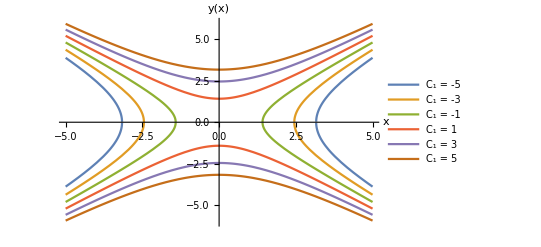

```mathematica
Show[Plot[Evaluate[Table[√(2 C+t^2),{C,-5,5,2}]],{t,-5,5},],
Plot[Evaluate[Table[-√(2 C+t^2),{C,-5,5,2}]],{t,-5,5},]]
```

For large positive and negative t values, this function behaves like ±|t|.

## Classify Equation as Separable

Substitute the solution back into the equation obtained after integration to show it is satisfied:

```mathematica
verify=(eqn/.sol)//Simplify
```

{True,True}

Since the solution contains two branches, use DSolve to get both branches:

```mathematica
dsln=DSolve[{y'[t]==t/y[t]},y[t],t]
```

{{y[t]→-√(t^2+2 C[1])},{y[t]→√(t^2+2 C[1])}}

The two solutions can be extracted using ReplaceAll (/.):

```mathematica
(y[t]/.dsln)
```

{-√(t^2+2 C[1]),√(t^2+2 C[1])}

## Solving Autonomous Equations

Verify that the following equation is separable and find its solution:

y'(t)=y(t)(5+y(t))

This is an example of an autonomous equation, which means that the equation does not explicitly depend on the independent variable t.

Whenever an equation is autonomous, it is guaranteed to be separable.

Simply divide both sides of the equation by the expression on the right and multiply both sides by ⅆt:

1/(y(t)(5+y(t)))ⅆy=1 ⅆt

Apply Integrate to both sides:

```mathematica
eqn=Integrate[1/(y[t] (5+y[t])),y[t]]==Integrate[1,t,GeneratedParameters->C]
```

1/5 Log[y[t]]-1/5 Log[5+y[t]]==t+C[1]

## Solving Autonomous Equations

To find the solution, use Solve on the equation for y(t):

```mathematica
sol=Solve[eqn,y[t]][[1]]
```

{y[t]→-(5 ⅇ^(5 t+5 C[1]))/(-1+ⅇ^(5 t+5 C[1]))}

Observe the function’s behavior for different values of C_1:

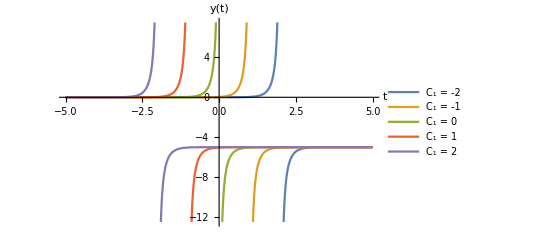

```mathematica
Plot[Evaluate[Table[-(5 ⅇ^(5 Subscript[C, 1]+5 t))/(-1+ⅇ^(5 Subscript[C, 1]+5 t)),{Subscript[C, 1],-2,2}]],{t,-5,5},]
```

For large positive t values, this function behaves like y=-5.

For large negative t values, this function behaves like y=0.

The function also has a vertical asymptote when t=-C.

## Solving Separable Equations

Use ReplaceAll to extract the solution found from Solve:

```mathematica
ySol=(y[t]/.sol)
```

-(5 ⅇ^(5 t+5 C[1]))/(-1+ⅇ^(5 t+5 C[1]))

Replace this solution into the differential equation and use Simplify to show it satisfies the equation:

```mathematica
(y'[t]==y[t] (5+y[t]))/.y->Function[t,Evaluate[ySol]]//Simplify
```

True

Find the result with DSolveValue:

```mathematica
dsln=DSolveValue[y'[t]==y[t] (5+y[t]),y[t],t]
```

-(5 ⅇ^(5 t+5 C[1]))/(-1+ⅇ^(5 t+5 C[1]))

Show that the result from DSolveValue agrees with the result found earlier:

```mathematica
ySol==dsln
```

True

## Example 1

Solve the initial value problem and determine where the solution attains its maximum value:

y'(t)=(2 cos(2 t))/(3+2 y(t))

y(0)=-1

By observation, it can be seen that this equation is not autonomous, but it is still separable.

This equation can be separated by multiplying both sides by (3+2 y(t))ⅆt:

(3+2 y(t))ⅆy(t)=2 cos(2 t)ⅆt

Both sides of the equation are integrable:

```mathematica
eqn=Integrate[3+2 y[t],y[t]]==Integrate[2 Cos[2 t],t,GeneratedParameters->C]
```

3 y[t]+y[t]^2==C[1]+Sin[2 t]

## Example 1

Now all that remains to find the solution is to solve for the unknown function y(t):

```mathematica
Solve[eqn,y[t]]
```

{{y[t]→1/2 (-3-√(9+4 C[1]+4 Sin[2 t]))},{y[t]→1/2 (-3+√(9+4 C[1]+4 Sin[2 t]))}}

This agrees with the output from DSolve:

```mathematica
DSolve[y'[t]==2Cos[2t]/(3+2y[t]),y[t],t]
```

{{y[t]→1/2 (-3-√(9+4 C[1]+4 Sin[2 t]))},{y[t]→1/2 (-3+√(9+4 C[1]+4 Sin[2 t]))}}

Plot the solution 1/2(-3+√(9+4 C_1+4 sin(2 t))) to see its behavior for different values of C_1:

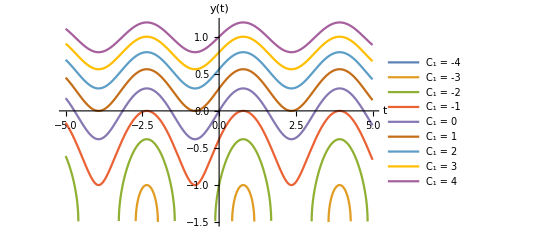

```mathematica
Plot[Evaluate[Table[1/2 (-3+√(9+4 C+4 Sin[2 t])),{C,-4,4}]],{t,-5,5},]
```

For this set of solutions, observe that the maximum occurs whenever sin(2 t) is maximized, which occurs when sin(2 t)=1:

```mathematica
Solve[Sin[2 t]==1,t]//Expand
```

{{t→ConditionalExpression[π/4+π C[1], C[1]∈ℤ]}}

Thus, the maximum occurs when t=π/4+π C_1 for any integer C_1.

## Summary

This lesson discussed a subclass of first-order differential equations called separable equations.

First-order differential equations can be classified as separable when the variables can be separated to different parts of the equation:

M(y(t))ⅆy(t)=N(t)ⅆt

Then, using integration, obtain that:

∫M(y(t))ⅆy(t)=∫N(t)ⅆt + C

This lesson also defined a class of differential equations that are autonomous.

For autonomous equations, the independent variable does not appear in the equation and so it is always separable.